```mathematica
Cauchy:
```

```mathematica
p = 1/(π*σ)(1+ ((x-μ)/σ)^2)^-1
```

1/(π (1+(x-μ)^2/σ^2) σ)

```mathematica
θ = σ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

1/σ-(2 σ)/((x-μ)^2+σ^2)

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

-1/σ^2+(4 σ^2)/(((x-μ)^2+σ^2)^2)-2/((x-μ)^2+σ^2)

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

π^(-1-α) (σ/((x-μ)^2+σ^2))^(1+α) (1/σ-(2 σ)/((x-μ)^2+σ^2))

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ]
```

(π^(-1-α) (-1+y^2) (1/(σ+y^2 σ))^α)/((1+y^2)^2 σ^2)

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[-(π^(-1/2-α) α (1/σ)^(1+α) Gamma[1/2+α])/Gamma[2+α],Re[α]>-1/2]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

π^(-1-α) (σ/((x-μ)^2+σ^2))^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ]
```

(1/(π σ+π y^2 σ))^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[(π^(-1/2-α) σ^-α Gamma[1/2+α])/Gamma[1+α],Re[α]>-1/2]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[-(α (1/σ)^α σ^(-1+α))/(1+α),α+Conjugate[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[(α (1/σ)^α σ^(-2+α))/(1+α),α+Conjugate[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[π^(-1-α) (σ/((x-μ)^2+σ^2))^(1+α) ((-1+α)/σ^2+(α (-1+2 α) (1/σ)^α σ^(-2+α))/(1+α)+(α^3 (1/σ)^(2 α) σ^(-2+2 α))/(1+α)^2+(4 (1+α) σ^2)/(((x-μ)^2+σ^2)^2)+(-2-4 α)/((x-μ)^2+σ^2)-(4 α^2 (1/σ)^α σ^α)/((1+α) ((x-μ)^2+σ^2))),α+Conjugate[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ]
```

ConditionalExpression[1/σ^2(1/(π σ+π y^2 σ))^(1+α) ((1+y^4 (-1+α)+α-2 y^2 (2+α))/((1+y^2)^2)+(α (-1-2 α+y^2 (-1+2 α)) (1/σ)^α σ^α)/((1+y^2) (1+α))+(α^3 (1/σ)^(2 α) σ^(2 α))/(1+α)^2),α+Conjugate[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ,{y,-∞,∞}]]
```

ConditionalExpression[(π^(-1/2-α) σ^(-2-α) (4^(1-α) √π (1/σ)^α σ^α (-1+α (-1+α (-2+(1/σ)^α σ^α))) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1])) Sec[π α])/(4 (1+α)^2 Gamma[α] Gamma[1+α]),α+Conjugate[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[-(4 √π (1+α)^2 σ^(2+α) (σ/((x-μ)^2+σ^2))^α (1/σ+(α (1/σ)^α σ^(-1+α))/(1+α)-(2 σ)/((x-μ)^2+σ^2)) Cos[π α] Gamma[α] Gamma[1+α])/(4^(1-α) √π (1/σ)^α σ^α (-1+α (-1+α (-2+(1/σ)^α σ^α))) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1])),α+Conjugate[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.μ->0]
```

ConditionalExpression[-(4 √π (1+α)^2 σ^(2+α) (σ/(x^2+σ^2))^α (1/σ+(α (1/σ)^α σ^(-1+α))/(1+α)-(2 σ)/(x^2+σ^2)) Cos[π α] Gamma[α] Gamma[1+α])/(4^(1-α) √π (1/σ)^α σ^α (-1+α (-1+α (-2+(1/σ)^α σ^α))) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1])),α+Conjugate[α]>-1]

```mathematica
IFun = Function[{σ,α} ,-(4 √π (1+α)^2 σ^(2+α) (σ/(x^2+σ^2))^α (1/σ+(α (1/σ)^α σ^(-1+α))/(1+α)-(2 σ)/(x^2+σ^2)) Cos[π α] Gamma[α] Gamma[1+α])/(4^(1-α) √π (1/σ)^α σ^α (-1+α (-1+α (-2+(1/σ)^α σ^α))) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1]))]
```

Function[{σ,α},-(4 √π (1+α)^2 σ^(2+α) (σ/(x^2+σ^2))^α (1/σ+(α (1/σ)^α σ^(-1+α))/(1+α)-(2 σ)/(x^2+σ^2)) Cos[π α] Gamma[α] Gamma[1+α])/(4^(1-α) √π (1/σ)^α σ^α (-1+α (-1+α (-2+(1/σ)^α σ^α))) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1]))]

```mathematica
FullSimplify[IFun[1,α]]
```

-(4 √π (1/(1+x^2))^α (1+α)^2 (1-2/(1+x^2)+α/(1+α)) Cos[π α] Gamma[α] Gamma[1+α])/(-4^(1-α) √π (1+α+α^2) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1]))

```mathematica
IFuns = Function[{α},-(4 √π (1/(1+x^2))^α (1+α)^2 (1-2/(1+x^2)+α/(1+α)) Cos[π α] Gamma[α] Gamma[1+α])/(-4^(1-α) √π (1+α+α^2) Cos[π α] Gamma[1+2 α]+1/(3 (3+4 α (2+α)))8 π (1+α) (-1+α (1+α)^2) Gamma[α] (6 (1+α) Hypergeometric2F1Regularized[1/2,2,1/2-α,1]-4^-α Gamma[4+2 α] Hypergeometric2F1Regularized[1/2+α,1+α,-1/2+α,1]))] // TraditionalForm
```

{α}↦-(4 √π (α+1)^2 cos(π α) α α+1 (1/(x^2+1))^α (α/(α+1)-2/(x^2+1)+1))/((8 π (α+1) (α (α+1)^2-1) α (6 (α+1) 1/221/2-α1-4^-α 2 α+4 α+1/2α+1α-1/21))/(3 (4 α (α+2)+3))-√π 4^(1-α) (α^2+α+1) cos(π α) 2 α+1)

```mathematica
FullSimplify[IFuns[1]]
```

({α}↦-(4 √π (α+1)^2 cos(π α) α α+1 (1/(x^2+1))^α (α/(α+1)-2/(x^2+1)+1))/((8 π (α+1) (α (α+1)^2-1) α (6 (α+1) 1/221/2-α1-4^-α 2 α+4 α+1/2α+1α-1/21))/(3 (4 α (α+2)+3))-√π 4^(1-α) (α^2+α+1) cos(π α) 2 α+1))[1]

```mathematica
Needs["PlotLegends`"]
```

```mathematica
Plot[{
(*IFun[1,0.05]
IFun[1,0.1],
IFun[1,0.3],
*)IFuns[1]
(*IFun[1,1],
IFun[1,2](1+α)^2 (x+x α-σ) (1/σ)^-α (ⅇ^(-x/σ)/σ)^α*)},
{x,0,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"}
]
```

```mathematica
Cauchy:
```

```mathematica
θ = μ
```

μ

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(2 (x-μ))/((x-μ)^2+σ^2)

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

(2 (x-μ)^2-2 σ^2)/(((x-μ)^2+σ^2)^2)

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

(2 π^(-1-α) (x-μ) σ (σ/((x-μ)^2+σ^2))^α)/(((x-μ)^2+σ^2)^2)

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ]
```

(2 π^(-1-α) y (1/(σ+y^2 σ))^α)/((1+y^2)^2 σ^2)

```mathematica
csIntCitatel3 = FullSimplify[Integrate[csIntCitatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[0,Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

π^(-1-α) (σ/((x-μ)^2+σ^2))^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ]
```

(1/(π σ+π y^2 σ))^(1+α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ,{y,-∞,∞}]]
```

ConditionalExpression[(π^(-1/2-α) σ^-α Gamma[1/2+α])/Gamma[1+α],Re[α]>-1/2]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[0,Re[α]>-1/2]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[0,Re[α]>-1/2]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[(2 π^(-1-α) σ ((1+2 α) (x-μ)^2-σ^2) (σ/((x-μ)^2+σ^2))^α)/(((x-μ)^2+σ^2)^3),α+Conjugate[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ]
```

ConditionalExpression[(2 π^(-1-α) (-1+y^2 (1+2 α)) (1/(σ+y^2 σ))^α)/((1+y^2)^3 σ^3),α+Conjugate[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ,{y,-∞,∞}]]
```

ConditionalExpression[-(2 π^(-1/2-α) (1/σ)^(2+α) Gamma[3/2+α])/Gamma[3+α],α+Conjugate[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(√π (x-μ) (1/σ)^(-1-α) (σ/((x-μ)^2+σ^2))^(1+α) Gamma[3+α])/Gamma[3/2+α],α+Conjugate[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.σ->1]
```

ConditionalExpression[(√π (1/(1+(x-μ)^2))^(1+α) (x-μ) Gamma[3+α])/Gamma[3/2+α],α+Conjugate[α]>-1]

```mathematica
IFun = Function[{μ,α} ,(√π (1/(1+(x-μ)^2))^(1+α) (x-μ) Gamma[3+α])/Gamma[3/2+α]];
```

```mathematica
Needs["PlotLegends`"]
```

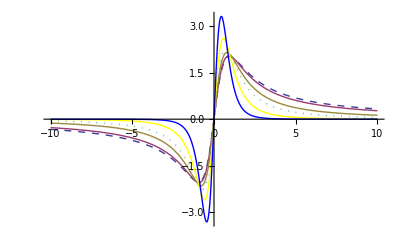

```mathematica
Plot[{
IFun[0,0.05],
IFun[0,0.1],
IFun[0,0.3],
IFun[0,0.5],
IFun[0,1],
IFun[0,2]},
{x,-10,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```